# Trajectories: curves in space

```mathematica
Hyperlink["Obsidian page of trajectories","obsidian://open?vault=PhysicsKB&file=Classical%20Mechanics%2FTrajectories"]
```

[Obsidian page of trajectories](obsidian://open?vault=PhysicsKB&file=Classical%20Mechanics%2FTrajectories)

## Drawing functions

```mathematica
Clear[trajectory,point]
point[r_,t_,color_:Orange]:=Module[{},
Which[
Length[r[t]]==3,Graphics3D[{color,PointSize[0.06],Point[r[t]]},BoxRatios->{1, 1, 1}],
Length[r[t]]==2,Graphics[{color,PointSize[0.06],Point[r[t]]}]
]
];
trajectory[r_,{t0_,t1_}]:=Module[{α},
Which[Length[r[α]]==3,ParametricPlot3D[r[t],{t,t0,t1},BoxRatios->{1, 1, 1}],Length[r[α]]==2,ParametricPlot[r[t],{t,t0,t1},ImageSize->Small]]
];
```

## Examples

### Non one-to-one

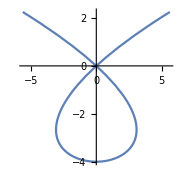

```mathematica
r[t_]:={t^3-4t,t^2-4};
{t0,t1}={-2.5,2.5};
trajectory[r,{t0,t1}]
Manipulate[Show[trajectory[r,{t0,t1}],point[r,t]],{t,t0,t1}]
```

### The cycloid

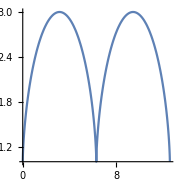

```mathematica
Clear[r1,r2,r]
r1[t_]:={t,1}
r2[t_]:={-Sin[t],1-Cos[t]}
r[t_]:=r1[t]+r2[t]
{t0,t1}={0,4π};
trajectory[r,{t0,t1}]
Manipulate[Show[trajectory[r,{t0,t1}],point[r,t]],{t,t0,t1}]
```